```mathematica
ClearAll["Global`*"];
```

## The Worker Problem

```mathematica
(*Set parameter values*)
alpha=0.1;(*Preference parameter*)
w=100;(*wage*)
p=20;(*Price of goods*)
hours=16;(*available hours (24-subsistence)*)
(*Define the utility function*)U[c_,l_]:=c^alpha*l^(1-alpha)
```

```mathematica
(*Define the Lagrangian*)
Lagrangian[c_,l_,lambda_]:=U[c,l]+lambda*(p*c-w(hours-l))
```

```mathematica
(*Set up the first-order conditions*)
eq1=D[Lagrangian[c,l,lambda],c]==0;
eq2=D[Lagrangian[c,l,lambda],l]==0;
eq3=p*c-w(hours-l)==0;
```

```mathematica
(*Solve the system of equations*)
solution=Solve[{eq1,eq2,eq3},{c,l,lambda}]
```

{{c→8.,l→14.4,lambda→-0.00848624}}

```mathematica
utilityStar=U[c/.solution, l/.solution][[1]];
cStar=c/.solution[[1]];
lStar=l/.solution[[1]];
mStar=w(hours-lStar);
List[utilityStar,cStar,lStar,mStar]
```

{13.578,8.,14.4,160.}

```mathematica
utilityPlot = Plot3D[
U[c,l],{c,0,2*mStar/p},{l,0,hours}
];
optimalBundle3D=Flatten[{cStar,lStar,utilityStar}];
optimalPoint3D[a_]:=
Graphics3D[
{Red,Ball[a,mStar/(10*(p))]}
];
```

```mathematica
Show[
utilityPlot,
 optimalPoint3D[optimalBundle3D]
]
```

-Graphics3D-

```mathematica
indiCurves = 
ContourPlot[
U[c,l],{l,0,24},{c,0,3*mStar/p},
Contours->5,
ContourShading->None,
PlotLegends->Automatic,
FrameLabel->{"Leisure","Consumption"},
PlotLabel->"Indifference Curves and the Worker's Budget Line"
];
```

```mathematica
maxIndiCurve=
ContourPlot[
U[c,l]==utilityStar,
{l,0,25},{c,0,3*mStar/p},
ContourStyle->Blue
];
```

```mathematica
budget=
Plot[
(hours-l)*w/p,{l,0,hours},
PlotStyle->Directive[Blue,Thick]
];
```

```mathematica
optimalBundle ={lStar,cStar}
```

{14.4,8.}

```mathematica
optimalPoint[a_]:=
Graphics[
{Red,PointSize[Large],Point[a]}
];
```

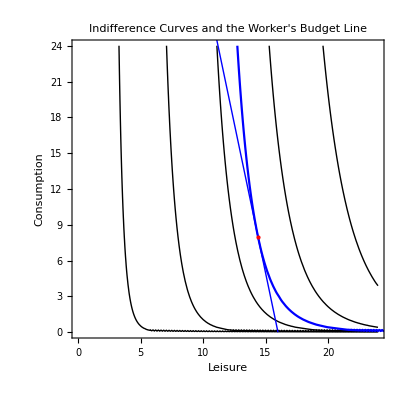

```mathematica
Show[
indiCurves,maxIndiCurve,budget, optimalPoint[optimalBundle]
]
```

```mathematica
Manipulate[] (*Changing alpha, wage and prices. Use CobbDouglas shortcut*)
```

Manipulate[]